# 1: Matrix-Vector Multiplication

We need to know how to get computers to build matrices and vectors and do all sorts of things to them.  Our matrices will mostly be real.

## Defining Matrices and Vectors

Random matrices are easy

```mathematica
{m,n}={6,5};
A=RandomReal[{-1,1},{m,n}];
b=RandomReal[{-1,1},n]
```

{-0.611644,0.0123107,-0.0562307,0.185501,-0.483318}

Typing in all the entries is a pain.

```mathematica
A={{1,2,3},{4,5,6},{7,8,9}};
b={11,12,13};
```

Importing things from the web (or anywhere else) is easy.

SparseArray[…]

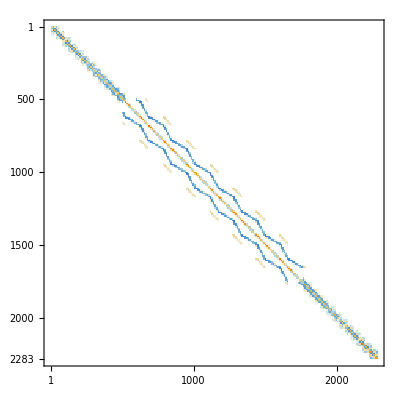

```mathematica
A=Import[
"https://math.nist.gov/pub/MatrixMarket2/SPARSKIT/fidap/fidap024.mtx.gz"]
MatrixPlot[A]
```

```mathematica
2
```

If the file is on your computer the “File Path” file browser under Insert is convenient.  You can also set a directory using “SetDirectory”

## Getting Bits of matrices

Matrix entries are easy: double square brackets

```mathematica
Dimensions[A]
```

{12,12}

Rows or columns use a span notation

```mathematica
b=A⟦2,1;;4⟧
b=Normal[b]
```

{0.270313,1.,0.899072,0.118814}

{0.270313,1.,0.899072,0.118814}

The “SparseArray” does not store the zeros.  The “Normal” vector does!

Sub matrices use the span notation twice! Matrices display flat. To get a pretty matrix use “MatrixForm”. 
You can NOT compute with the pretty version!

```mathematica
ASub=Normal[A⟦1;;4,1;;10⟧]
MatrixForm[ASub]
```

{{1.,0.270313,0.512484,0.648836,0.243861,0.562201,0.962043,0.0520912,0.160216,0.272761},{0.270313,1.,0.899072,0.118814,0.978073,0.857536,0.184355,0.105131,0.915916,0.823316},{0.512484,0.899072,1.,0.252959,0.858364,0.992122,0.385166,0.113642,0.726082,0.787059},{0.648836,0.118814,0.252959,1.,0.088126,0.26102,0.559241,0.163724,0.0494527,0.213914}}

(1. | 0.270313 | 0.512484 | 0.648836 | 0.243861 | 0.562201 | 0.962043 | 0.0520912 | 0.160216 | 0.272761
0.270313 | 1. | 0.899072 | 0.118814 | 0.978073 | 0.857536 | 0.184355 | 0.105131 | 0.915916 | 0.823316
0.512484 | 0.899072 | 1. | 0.252959 | 0.858364 | 0.992122 | 0.385166 | 0.113642 | 0.726082 | 0.787059
0.648836 | 0.118814 | 0.252959 | 1. | 0.088126 | 0.26102 | 0.559241 | 0.163724 | 0.0494527 | 0.213914)

## Multiplying Matrices and Vectors

In Mathematica a dot means matrix-vector and matrix-matrix multiplication

```mathematica
{m,n}={6,5};
A=RandomReal[{-1,1},{m,n}];
b=RandomReal[{-1,1},n];
A.b
```

{0.64571,-0.753365,-0.389241,0.176365,0.589214,0.299523}

You get a warning if dimensions do not match!

```mathematica
{m,n}={6,5};
A=RandomReal[{-1,1},{m,n}];
b=RandomReal[{-1,1},m];
A.b
```

Dot::dotsh: Tensors {{-0.497646,-0.12317,-0.273019,-0.47798,0.722175},«4»,{0.97559,0.150869,0.554334,-0.718004,-0.143689}} and {-0.142328,0.491866,-0.87372,0.832738,0.984187,-0.0862579} have incompatible shapes.

{{-0.497646,-0.12317,-0.273019,-0.47798,0.722175},{0.0119647,0.970378,-0.878201,-0.126754,-0.455364},{0.943591,0.0483172,0.692733,0.824927,-0.222679},{-0.811524,0.195105,-0.589158,-0.281803,0.0445548},{0.126624,-0.0617333,0.74385,0.591444,0.824739},{0.97559,0.150869,0.554334,-0.718004,-0.143689}}.{-0.142328,0.491866,-0.87372,0.832738,0.984187,-0.0862579}

It works the same for matrix-matrix multiplication

```mathematica
{m,n,r}={6,5,12};
A=RandomReal[{-1,1},{m,n}];
B=RandomReal[{-1,1},{n,r}];
Dimensions[A.B]
```

{6,12}

## Multiplying Matrices from scratch: Efficiency!

You can define matrix-matrix multiplication C=A.B from C_(i,j)=∑_k A_(i,k)B_(k,j) if you want but it is going to be slower (in every way you can imagine) than the built in command!

```mathematica
{m,n,r}={6,5,12};
A=RandomReal[{-1,1},{m,n}];
B=RandomReal[{-1,1},{n,r}];
CBuiltIn=A.B;
CFormula=Table[
Sum[A⟦i,k⟧B⟦k,j⟧,{k,n}],
{i,m},{j,r}];
Norm[CBuiltIn-CFormula]
```

0.

We can race the two versions!

```mathematica
{m,n,r}={160,150,112};
A=RandomReal[{-1,1},{m,n}];
B=RandomReal[{-1,1},{n,r}];
Timing[CBuiltIn=A.B;]
Timing[CFormula=Table[
Sum[A⟦i,k⟧B⟦k,j⟧,{k,n}],
{i,m},{j,r}];]
Norm[CBuiltIn-CFormula]
```

{0.,Null}

{2.5625,Null}

3.15774×10^-14

## Assembling/Disassembling Matrices

We will frequently want to disassemble matrices and/or build matrices out of other matrices or vectors! For example, in the book we think of A is a bunch columns
	A=[a_1|a_2|…|a_n]

```mathematica
{m,n}={3,4};
A=RandomReal[{-1,1},{m,n}];
MatrixForm[A]
A⟦All,1⟧
A⟦1,All⟧
```

(-0.873592 | 0.0552016 | 0.758583 | -0.0042804
0.11646 | -0.812307 | -0.559926 | -0.81953
0.555716 | -0.035729 | 0.197457 | 0.939097)

{-0.873592,0.11646,0.555716}

{-0.873592,0.0552016,0.758583,-0.0042804}

The book encourages us to think of 
	C=A.B=[A.b_1|A.b_2|…]
We can check this as follows

```mathematica
{m,n,r}={3,2,4};
A=RandomReal[{-1,1},{m,n}];B=RandomReal[{-1,1},{n,r}];
CBuiltIn=A.B;
CCols=Table[A.B⟦All,j⟧,{j,r}]ᵀ;
Map[MatrixForm,{CBuiltIn,CCols}]
```

{(1.02453 | -0.28856 | 0.75057 | 1.11341
1.04663 | 0.151969 | 0.62859 | 0.838736
-0.810314 | 0.400194 | -0.646819 | -0.995586),(1.02453 | -0.28856 | 0.75057 | 1.11341
1.04663 | 0.151969 | 0.62859 | 0.838736
-0.810314 | 0.400194 | -0.646819 | -0.995586)}

We can race the two versions!

```mathematica
{m,n,r}={132,422,244};
A=RandomReal[{-1,1},{m,n}];B=RandomReal[{-1,1},{n,r}];
Timing[CBuiltIn=A.B;]
Timing[CCols=Table[A.B⟦All,j⟧,{j,r}]ᵀ;]
Norm[CBuiltIn-CCols]
```

{0.,Null}

{0.,Null}

9.60806×10^-14

## Block Matrices and Blocks of Matrices

A block matrix 
	A=(A_11 | A_12
A_21 | A_22
A_31 | A_33)
simply slams matrices (of matching dimensions) together.

```mathematica
{m,n}={2,3};
{{A11,A12},
{A21,A22},
{A31,A32}}=RandomReal[{-1,1},{3,2,m,n}];
A=ArrayFlatten[{{A11,A12},{A21,A22},{A31,A32}}];
Dimensions[A];
Map[MatrixForm,{A,A31}]
```

{(-0.860021 | 0.57662 | -0.0612185 | -0.514341 | -0.168068 | -0.658969
0.205342 | 0.584537 | -0.390041 | -0.896421 | -0.712405 | 0.00373995
-0.0457778 | -0.109664 | -0.773798 | -0.194606 | -0.257679 | -0.563672
0.350638 | 0.667973 | -0.558637 | -0.771917 | 0.247972 | -0.601144
0.294296 | -0.16399 | -0.557411 | 0.55366 | 0.885239 | -0.442101
-0.499133 | 0.375626 | -0.497032 | 0.594444 | -0.411685 | 0.950597),(0.294296 | -0.16399 | -0.557411
-0.499133 | 0.375626 | -0.497032)}

You can grab a chunk of a matrix using the range notation

```mathematica
Map[MatrixForm,{A[[1;;m,1;;n]],A11}]
```

{(-0.860021 | 0.57662 | -0.0612185
0.205342 | 0.584537 | -0.390041),(-0.860021 | 0.57662 | -0.0612185
0.205342 | 0.584537 | -0.390041)}

## Inverse Matrices and Linear Solves

Almost all random square matrices A have an inverse A^-1 satisfying A^-1.A=Id

```mathematica
m=23;
A=RandomReal[{-1,1},{m,m}];
AInv=Inverse[A];
Norm[A.AInv-IdentityMatrix[m]]
```

1.8393×10^-13

Most of the time you do not want the inverse! You just want to solve the system A.x=b

```mathematica
m=1234;
A=RandomReal[{-1,1},{m,m}]; b=RandomReal[{-1,1},m];
Timing[AInv=Inverse[A]; bSlow=AInv.b;]
Timing[bFast=LinearSolve[A,b];]
Norm[bSlow-bFast]
```

{0.0625,Null}

{0.03125,Null}

2.75782×10^-12